```mathematica
n=1000; (*Number of entities*)

r:=RandomInteger[{1,n}]; (*r is a function that returns a random entity*)

f:=(#/(.01+Sqrt[Dot[#,#]]))&/@ (*Divide each vector (from next line) by (.01 + it's length) *)
(x[[#]]-x)&; (*An array of vectors from every point to a selected point*)
(*The function f returns an array of vectors. These vectors point from every entity towards a specified entity. The magnitude of these vectors is slightly less than that of a unit vector, and tends to zero as the distance between entities gets smaller*)

s:=With[{r1=r},p[[r1]]=r;q[[r1]]=r];(*for a random entity (the same random element in the p and q lists), s is a function to pick a new "friend" p and "enemy" q*)

x=RandomReal[{-1,1},{n,2}];(*x is an array of random real numbers in the range {-1,1}. There are two array elements for each entity. These are the initial coordinates of each entity.*)

{p,q}=RandomInteger[{1,n},{2,n}]; (*p and q are random entities at initialisation*)

Graphics[{PointSize[0.007], (*Create a point cloud*)
Dynamic[ (*Run this in real-time: *)
If[r<100,s];(*If a randomly chosen entity has ID < 100 (10% chance), run s *)
Point[x=0.995 x (*Multiply coordinates by 0.995 to move 5% closer to center*)
+0.02 f[p] (*Move (0.02 * vector length) units closer to "friend" p*)
-0.01 f[q]] (*Move (0.01 * vector length) units away from "enemy" q*)
]},
PlotRange->2](*set the range of the graphic*)
```

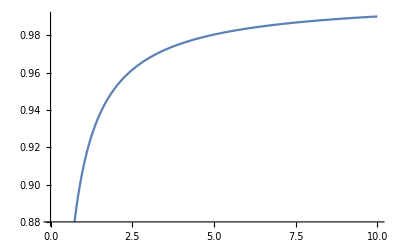

```mathematica
h=u/(0.1+u); (*How vector length in f varies with distance between points *)
Plot[h,{u,0,10}]
```